```mathematica
(y^-1)^-s/.s->3
```

y^3

```mathematica
y^s/.s->3
```

y^3

```mathematica
(y^-1)(y^s)
```

y^(-1+s)

```mathematica
(y^-3)(y^{3s})
```

{y^(-3+3 s)}

```mathematica
Dy[n_,s_, y_,k_]:=y^-1 Sum[( (1+j/ y))^-s Dy[n (1+j/ y)^-1,s, y,k-1],{j,1,(n-1)y}]
Dy[n_,s_, y_,0]:=UnitStep[n-1]
Dd[n_,s_, y_, k_]:=Sum[(j+y)^-s Dd[n(y+j)^-1,s,y, k-1],{j,0,n-y}]
Dd[n_,s_, y_, 0]:=UnitStep[n-1]
Cc[n_,s_, y_, k_]:=y^(k(s-1)) Dd[n y^k,s,y+1,k]
```

```mathematica
N[Dy[100,0,2,2]]
```

318.

```mathematica
N[Cc[100,0, 2,2]]
```

318.

```mathematica
D2a[n_,k_,s_]:=D2a[n,k,s]=Sum[j^(-s)D2a[Floor[n/j],k-1,s],{j,2,n}]
D2a[n_,0,s_]:=1
E2a[n_,k_, a_,s_]:= E2a[n,k,a,s]=Sum[ j^(-s)E2a[n/j,k-1,a,s],{j,2,n}]-a Sum[ (j a)^(-s)E2a[n/(a j),k-1,a,s],{j,1,n/a}]
E2a[n_,0,a_,s_]:=1
D2E2[n_,s_, k_,b_]:= Sum[ (-1)^j b^(j(1-s)) Binomial[k,j] Sum[ Binomial[j,m] If[n/b^j<1,0,D2a[n/b^j,k-m,s]],{m,0,j}],{j,0,k}]
E2D2[n_,s_, k_,b_]:= (-1)^k+Sum[b^(a(1-s))/((k-1)!) Binomial[k,j]Pochhammer[a-k+j+1,k-1]E2a[b^-a n,j,b,s],{a,0,Log[b,n]},{j,0,k}]
```

```mathematica
E2D2[100,0,2,2]
```

283

```mathematica
D2a[n_,k_,s_]:=Sum[j^(-s)D2a[Floor[n/j],k-1,s],{j,2,n}]
D2a[n_,0,s_]:=UnitStep[n-1]
E2a[n_,k_, x_,s_]:=Sum[ j^(-s)E2a[n/j,k-1,x,s],{j,2,n}]-x Sum[ (j x)^(-s)E2a[n/(x j),k-1,x,s],{j,1,n/x}]
E2a[n_,0,x_,s_]:=UnitStep[n-1]
D2E2[n_,s_, k_,x_]:= Sum[ (-1)^j x^(j(1-s)) Binomial[k,j] Sum[ Binomial[j,m] If[n/x^j<1,0,D2a[n/x^j,k-m,s]],{m,0,j}],{j,0,k}]
E2D2[n_,s_, k_,x_]:= (-1)^k+Sum[x^(a(1-s))/((k-1)!) Binomial[k,j]Pochhammer[a-k+j+1,k-1]E2a[x^-a n,j,x,s],{a,0,Log[x,n]},{j,0,k}]
{E2D2[100,-1,2,2],D2a[100,2,-1],D2E2[100,-1,2,2],E2a[100,2,2,-1]}
```

{16780,16780,276,276}

```mathematica
D2a[n_,k_,s_]:=Sum[j^(-s)D2a[Floor[n j^-1],k-1,s],{j,2,n}]
D2a[n_,0,s_]:=UnitStep[n-1]
E2a[n_,k_, x_,s_]:=Sum[ j^(-s)E2a[n j^-1,k-1,x,s],{j,2,n}]-x Sum[ (j x)^(-s)E2a[n (x j)^-1,k-1,x,s],{j,1,n x^-1}]
E2a[n_,0,x_,s_]:=UnitStep[n-1]
D2E2[n_,s_, k_,x_]:= Sum[ (-1)^j x^(j(1-s)) Binomial[k,j] Sum[ Binomial[j,m] D2a[n x^-j,k-m,s],{m,0,j}],{j,0,k}]
E2D2[n_,s_, k_,x_]:= (-1)^k+Sum[x^(a(1-s))/((k-1)!) Binomial[k,j]Pochhammer[a-k+j+1,k-1]E2a[x^-a n,j,x,s],{a,0,Log[x,n]},{j,0,k}]
{E2D2[100,-1,2,2],D2a[100,2,-1],D2E2[100,-1,2,2],E2a[100,2,2,-1]}
```

{16780,16780,276,276}

```mathematica
D2a[n_,s_, k_]:=Sum[j^(-s)D2a[Floor[n j^-1],s,k-1],{j,2,n}]
D2a[n_,s_,0]:=UnitStep[n-1]
E2a[n_,s_, k_, x_]:=Sum[ j^(-s)E2a[n j^-1,s,k-1,x],{j,2,n}]-x Sum[ (j x)^(-s)E2a[n (x j)^-1,s,k-1,x],{j,1,n x^-1}]
E2a[n_,s_, 0,x_]:=UnitStep[n-1]
D2E2[n_,s_, k_,x_]:= Sum[ (-1)^j x^(j(1-s)) Binomial[k,j] Binomial[j,m] D2a[n x^-j,s,k-m],{j,0,k},{m,0,j}]
E2D2[n_,s_, k_,x_]:= (-1)^k+Sum[x^(j(1-s)) Binomial[k,m]Binomial[m+j-1,k-1]E2a[n x^-j,s,m,x],{j,0,Log[x,n]},{m,0,k}]
{E2D2[100,-1,4,2],D2a[100,-1,4],D2E2[100,-1,4,2],E2a[100,-1,4,2]}
```

{13441,13441,-799,-799}

```mathematica
D2a[n_,s_, k_]:=Sum[j^(-s)D2a[Floor[n j^-1],s,k-1],{j,2,n}]
D2a[n_,s_,0]:=UnitStep[n-1]
E2a[n_,s_, k_, x_]:=Sum[ j^(-s)E2a[n j^-1,s,k-1,x],{j,2,n}]-x Sum[ (j x)^(-s)E2a[n (x j)^-1,s,k-1,x],{j,1,n x^-1}]
E2a[n_,s_, 0,x_]:=UnitStep[n-1]
D2E2[n_,s_, k_,x_]:= Sum[ (-1)^j x^(j(1-s)) Binomial[k,j] Binomial[j,m] D2a[n x^-j,s,k-m],{j,0,k},{m,0,j}]
E2D2[n_,s_, k_,x_]:= (-1)^k+Sum[x^(j(1-s)) Binomial[k,m]Binomial[m+j-1,k-1]E2a[n x^-j,s,m,x],{j,0,Log[x,n]},{m,0,k}]
{E2D2[100,-1,4,2],D2a[100,-1,4],D2E2[100,-1,4,2],E2a[100,-1,4,2]}
```

{13441,13441,-799,-799}

```mathematica
Table[ {Expand[(-1)^j Binomial[-z,j]]- Expand[Binomial[z+j-1,j]]},{j,0,5}]//TableForm
```

0
0
0
0
0
0

```mathematica
D2a[n_,s_, k_]:=Sum[j^(-s)D2a[Floor[n j^-1],s,k-1],{j,2,n}]
D2a[n_,s_,0]:=UnitStep[n-1]
E2a[n_,s_, k_, x_]:=Sum[ j^(-s)E2a[n j^-1,s,k-1,x],{j,2,n}]-x Sum[ (j x)^(-s)E2a[n (x j)^-1,s,k-1,x],{j,1,n x^-1}]
E2a[n_,s_, 0,x_]:=UnitStep[n-1]
D2E2[n_,s_, k_,x_]:= Sum[ (-1)^j x^(j(1-s)) Binomial[k,j] Binomial[j,m] D2a[n x^-j,s,k-m],{j,0,k},{m,0,j}]
E2D2[n_,s_, k_,x_]:= (-1)^k+Sum[(-1)^(k-1)x^(j(1-s)) Binomial[k,k-m]Binomial[m-j-1,k-1]E2a[n x^-j,s,k-m,x],{j,0,Log[x,n]},{m,0,k}]
{E2D2[120,2,4,3/2],D2a[120,2,4],D2E2[100,-1,4,2],E2a[100,-1,4,2]}
```

{518378950339973/8414884558080000,518378950339973/8414884558080000,-799,-799}

```mathematica
th[n_, k_] := FullSimplify[MangoldtLambda[ n ] / Log[n]] - n/Log[k,n] ( 1 + Floor[ Floor[ Log[k,n]]-Log[k,n]])
```

```mathematica
ts[n_, s_, 0] := UnitStep[n-1]
ts[n_, s_, k_] := Sum[ th[j,2] j^-s ts[ n/j, s, k-1],{j,2,n}]
```

```mathematica
ts[100,-1,1]
```

10301/60

```mathematica
th[n_, k_, b_] := (Floor[n/b]-Floor[(n-1)/b])FullSimplify[MangoldtLambda[ n/b ] / Log[n/b]] - n/b/Log[k,n/b] ( 1 + Floor[ Floor[ Log[k,n/b]]-Log[k,n/b]])
```

```mathematica
Table[{n/2,th[n,2,2]},{n,3,20}]
```

{{3/2,0},{2,-1},{5/2,0},{3,1},{7/2,0},{4,-3/2},{9/2,0},{5,1},{11/2,0},{6,0},{13/2,0},{7,1},{15/2,0},{8,-7/3},{17/2,0},{9,1/2},{19/2,0},{10,0}}

```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
aa[f_, n_, k_] := aa[f,n,k]=Sum[ f[j] aa[f, n/j, k-1],{j,2,n}]
aa[f_, n_, 0] := UnitStep[n-1]
aaz[f_, n_, z_] := Sum[bin[z,k] aa[f,n,k],{k,0,Log[2,n]}]
laaz[f_, n_] := D[aaz[f,n,z],z]/.z->0
bb[f_, n_, k_] := bb[f,n,k]=Sum[(-1)^(j+1) f[j]  bb[f,n/j, k-1],{j,2,n}]
bb[f_, n_, 0] := UnitStep[n-1]
bbz[f_, n_, z_] := Sum[bin[z,k] bb[f,n,k],{k,0,Log[2,n]}]
lbbz[f_, n_] := D[bbz[f,n,z],z]/.z->0
```

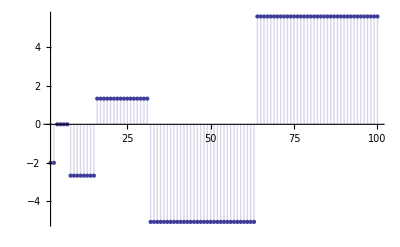

```mathematica
DiscretePlot[laaz[LiouvilleLambda,n]-lbbz[LiouvilleLambda,n],{n,2,100}]
```

```mathematica
Table[{(laaz[EulerPhi,n]-lbbz[EulerPhi,n]), Sum[(3^j-1)/j,{j,1,Log[2,n]}]},{n,2,20}]//TableForm
```

2 | 2
2 | 2
6 | 6
6 | 6
6 | 6
6 | 6
44/3 | 44/3
44/3 | 44/3
44/3 | 44/3
44/3 | 44/3
44/3 | 44/3
44/3 | 44/3
44/3 | 44/3
44/3 | 44/3
104/3 | 104/3
104/3 | 104/3
104/3 | 104/3
104/3 | 104/3
104/3 | 104/3

```mathematica
Table[{laaz[LiouvilleLambda,n]-lbbz[LiouvilleLambda,n], Sum[ ((-2)^j)/j,{j,1,Log[2,n]}]},{n,120,130}]//TableForm
```

28/5 | 28/5
28/5 | 28/5
28/5 | 28/5
28/5 | 28/5
28/5 | 28/5
28/5 | 28/5
28/5 | 28/5
28/5 | 28/5
-444/35 | -444/35
-444/35 | -444/35
-444/35 | -444/35

```mathematica
idd[n_] := 1
Table[{2^n,(laaz[ff=MoebiusMu,jj=2^n]-lbbz[ff,jj])-(laaz[ff,jj-1]-lbbz[ff,jj-1]), -2/n(1-Floor[n/2]+Floor[(n-1)/2])},{n,1,10}]//TableForm
```

2 | -2 | -2
4 | 0 | 0
8 | -2/3 | -2/3
16 | 0 | 0
32 | -2/5 | -2/5
64 | 0 | 0
128 | -2/7 | -2/7
256 | 0 | 0
512 | -2/9 | -2/9
1024 | 0 | 0

```mathematica
Table[{2^n,(laaz[ff=EulerPhi,jj=2^n]-lbbz[ff,jj])-(laaz[ff,jj-1]-lbbz[ff,jj-1]), (3^n-1)/n},{n,1,10}]//TableForm
```

2 | 2 | 2
4 | 4 | 4
8 | 26/3 | 26/3
16 | 20 | 20
32 | 242/5 | 242/5
64 | 364/3 | 364/3
128 | 2186/7 | 2186/7
256 | 820 | 820
512 | 19682/9 | 19682/9
1024 | 29524/5 | 29524/5

```mathematica
idc[n_] := DivisorSigma[1,n]
Table[{2^n,(laaz[ff=idc,jj=2^n]-lbbz[ff,jj])-(laaz[ff,jj-1]-lbbz[ff,jj-1]), (2^n)/n},{n,1,10}]//TableForm
```

2 | 6 | 2
4 | 14 | 2
8 | 48 | 8/3
16 | 188 | 4
32 | 3936/5 | 32/5
64 | 10304/3 | 32/3
128 | 107904/7 | 128/7
256 | 70624 | 32
512 | 328704 | 512/9
1024 | 7745024/5 | 512/5

```mathematica
ide[n_] := 1
Table[{2^n,(laaz[ff=ide,jj=2^n]-lbbz[ff,jj])-(laaz[ff,jj-1]-lbbz[ff,jj-1]), (2^n)/n},{n,1,10}]//TableForm
```

2 | 2 | 2
4 | 2 | 2
8 | 8/3 | 8/3
16 | 4 | 4
32 | 32/5 | 32/5
64 | 32/3 | 32/3
128 | 128/7 | 128/7
256 | 32 | 32
512 | 512/9 | 512/9
1024 | 512/5 | 512/5